```mathematica
σy=PauliMatrix[2]
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
σy.{1,0}
```

{0,ⅈ}

```mathematica
σy.{0,1}
```

{-ⅈ,0}

```mathematica
M={{2,2,2},{2,-1,1},{2,1,-1}};
```

```mathematica
Eigenvalues[M]
```

{4,-2,-2}

```mathematica
p1={2,1,1}/Norm[{2,1,1}];
```

```mathematica
p2={1,-1,-1}/Norm[{1,-1,-1}];
```

```mathematica
p3={0,1,-1}/Norm[{0,1,-1}];
```

```mathematica
Dot[p1,p2]
```

0

```mathematica
Dot[p2,p3]
```

0

```mathematica
Dot[p3,p1]
```

0

```mathematica
Dot[p1,p1]
```

1

```mathematica
Dot[p2,p2]
```

1

```mathematica
Dot[p3,p3]
```

1

```mathematica
M1=KroneckerProduct[p1,p1]
```

{{2/3,1/3,1/3},{1/3,1/6,1/6},{1/3,1/6,1/6}}

```mathematica
M2=KroneckerProduct[p2,p2]
```

{{1/3,-1/3,-1/3},{-1/3,1/3,1/3},{-1/3,1/3,1/3}}

```mathematica
M3=KroneckerProduct[p3,p3]
```

{{0,0,0},{0,1/2,-1/2},{0,-1/2,1/2}}

```mathematica
4*M1-2M2-2M3
```

{{2,2,2},{2,-1,1},{2,1,-1}}

```mathematica
M1+M2+M3
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
M1.M2
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
M2.M3
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
M3.M1
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
ψ=(2/3)*p1+(2/3)*p2-(1/3)*p3;
```

```mathematica
Transpose[ψ].M1.ψ//FullSimplify
```

4/9

```mathematica
Transpose[ψ].M2.ψ + Transpose[ψ].M3.ψ//FullSimplify
```

5/9

```mathematica
Jz={{1,0,0},{0,0,0},{0,0,-1}};
```

```mathematica
Jx=(1/Sqrt[2])*{{0,1,0},{1,0,1},{0,1,0}};
```

```mathematica
Jy=(1/Sqrt[2])*{{0,-I,0},{I,0,-I},{0,I,0}};
```

```mathematica
Jx.Jz-Jz.Jx
```

{{0,-1/(√2),0},{1/(√2),0,-1/(√2)},{0,1/(√2),0}}

```mathematica
(*[Jx^2,Jy^2]*)
```

```mathematica
(Jx.Jx).(Jy.Jy)-(Jy.Jy).(Jx.Jx)
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(*[Jy^2,Jz^2]*)
```

```mathematica
(Jy.Jy).(Jz.Jz)-(Jz.Jz).(Jy.Jy)
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(*[Jz^2,Jx^2]*)
```

```mathematica
(Jz.Jz).(Jx.Jx)-(Jx.Jx).(Jz.Jz)
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Jx2=Jx.Jx;
```

```mathematica
Jy2=Jy.Jy;
```

```mathematica
Jz2=Jz.Jz;
```

```mathematica
Jx2
```

{{1/2,0,1/2},{0,1,0},{1/2,0,1/2}}

```mathematica
Jy2
```

{{1/2,0,-1/2},{0,1,0},{-1/2,0,1/2}}

```mathematica
Jz^2
```

{{1,0,0},{0,0,0},{0,0,1}}

```mathematica
plus=(1/Sqrt[2]){1,0,1};
```

```mathematica
minus=(1/Sqrt[2])*{1,0,-1};
```

```mathematica
zero={0,1,0};
```

```mathematica
Jx2.plus
```

{1/(√2),0,1/(√2)}

```mathematica
Jx2.minus
```

{0,0,0}

```mathematica
Jx2.zero
```

{0,1,0}

```mathematica
Jy2.plus
```

{0,0,0}

```mathematica
Jy2.minus
```

{1/(√2),0,-1/(√2)}

```mathematica
Jy2.zero
```

{0,1,0}

```mathematica
Jz2.plus
```

{1/(√2),0,1/(√2)}

```mathematica
Jz2.minus
```

{1/(√2),0,-1/(√2)}

```mathematica
Jz2.zero
```

{0,0,0}

```mathematica
Jx.Jx+Jy.Jy+Jz.Jz
```

{{2,0,0},{0,2,0},{0,0,2}}

```mathematica
(*Problem 4*)
```

```mathematica
Id={{1,0},{0,1}};
```

```mathematica
σx={{0,1},{1,0}};
```

```mathematica
SX=(1/2)*(KroneckerProduct[σx,Id]+KroneckerProduct[Id,σx])
```

{{0,1/2,1/2,0},{1/2,0,0,1/2},{1/2,0,0,1/2},{0,1/2,1/2,0}}

```mathematica
SX.{1,0,0,0}
```

{0,1/2,1/2,0}

```mathematica
SX.{0,1,1,0}/Sqrt[2]
```

{1/(√2),0,0,1/(√2)}

```mathematica
U={{0,1,0,0},1/Sqrt[2]*{1,0,1,0},1/Sqrt[2]*{-1,0,1,0},{0,0,0,1}};
```

```mathematica
ConjugateTranspose[U].SX.U
```

{{0,0,0,0},{0,0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,0,1/(√2),0}}

```mathematica
(*Problem 5a*)
```

```mathematica
(*define input states*)
```

```mathematica
v0={1,0};
```

```mathematica
v1={-1/2,Sqrt[3]/2};
```

```mathematica
v2={-1/2,-Sqrt[3]/2};
```

```mathematica
(*define measurement basis*)
```

```mathematica
A={Cos[θ],Sin[θ]};
B={-Sin[θ],Cos[θ]};
```

```mathematica
(*calculate inner products*)
```

```mathematica
A0=Dot[A,v0]^2//FullSimplify
```

Cos[θ]^2

```mathematica
B0=Dot[B,v0]^2//FullSimplify
```

Sin[θ]^2

```mathematica
A1=Dot[A,v1]^2//FullSimplify
```

1/4 (Cos[θ]-√3 Sin[θ])^2

```mathematica
B1=Dot[B,v1]^2//FullSimplify
```

1/4 (√3 Cos[θ]+Sin[θ])^2

```mathematica
A2=Dot[A,v2]^2//FullSimplify
```

1/4 (Cos[θ]+√3 Sin[θ])^2

```mathematica
B2=Dot[B,v2]^2//FullSimplify
```

1/4 (-√3 Cos[θ]+Sin[θ])^2

```mathematica
2/3+1/2
```

7/6

```mathematica
Cos[θ]^2/((Cos[θ]^2+1/4 (Cos[θ]-√3 Sin[θ])^2+1/4 (Cos[θ]+√3 Sin[θ])^2))//FullSimplify
```

(2 Cos[θ]^2)/3

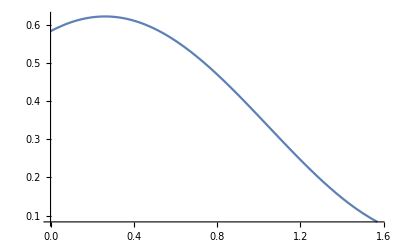

```mathematica
Plot[Cos[θ]^2/(2*(Cos[θ]^2+1/4 (Cos[θ]-√3 Sin[θ])^2+1/4 (Cos[θ]+√3 Sin[θ])^2))+(1/2)*(Max[1/4 (√3 Cos[θ]+Sin[θ])^2,1/4 (-√3 Cos[θ]+Sin[θ])^2])/(Sin[θ]^2+1/4 (√3 Cos[θ]+Sin[θ])^2+1/4 (-√3 Cos[θ]+Sin[θ])^2),{θ,0,Pi/2}]
```

```mathematica
N[Pi/12]
```

0.261799

```mathematica
FindMaxValue[Cos[θ]^2/(2*(Cos[θ]^2+1/4 (Cos[θ]-√3 Sin[θ])^2+1/4 (Cos[θ]+√3 Sin[θ])^2))+(1/2)*(Max[1/4 (√3 Cos[θ]+Sin[θ])^2,1/4 (-√3 Cos[θ]+Sin[θ])^2])/(Sin[θ]^2+1/4 (√3 Cos[θ]+Sin[θ])^2+1/4 (-√3 Cos[θ]+Sin[θ])^2),θ]
```

0.622008

```mathematica
(*if pick second basis vector as indicator*)
(*calculate success probabilities*)
```

```mathematica
PrBv0=B0/(B0+B1+B2)//FullSimplify
```

(2 Sin[θ]^2)/3

```mathematica
PrBv1=B1/(B0+B1+B2)//FullSimplify
```

1/6 (√3 Cos[θ]+Sin[θ])^2

```mathematica
PrBv2=B2/(B0+B1+B2)//FullSimplify
```

1/6 (-√3 Cos[θ]+Sin[θ])^2

```mathematica
(*if pick first basis vector as indicator*)
(*calculate success probabilities*)
```

```mathematica
PrAv0=A0/(A0+A1+A2)//FullSimplify
```

(2 Cos[θ]^2)/3

```mathematica
PrAv1=A1/(A0+A1+A2)//FullSimplify
```

1/6 (Cos[θ]-√3 Sin[θ])^2

```mathematica
PrAv2=A2/(A0+A1+A2)//FullSimplify
```

1/6 (Cos[θ]+√3 Sin[θ])^2

```mathematica
N[350/600]
```

0.583333

```mathematica
(*find Max*)
```

```mathematica
MaxValue[PrAv0,θ]
```

2/3

```mathematica
MaxValue[PrAv1,θ]
```

2/3

```mathematica
MaxValue[PrAv2,θ]
```

2/3

```mathematica
MaxValue[PrBv0,θ]
```

2/3

```mathematica
MaxValue[PrBv1,θ]
```

2/3

```mathematica
MaxValue[PrBv2,θ]
```

2/3

```mathematica
(*5b*)
```

```mathematica
a1={0,0,0,1};
a3={α,β,0,0};
```

```mathematica
a2={-α/2,β,α*Sqrt[3]/2,0};
```

```mathematica
a4={-α/2,β,-α*Sqrt[3]/2,0};
```

```mathematica
Psi1={1,0,0,0};
```

```mathematica
Psi2 = {-1/2,0,Sqrt[3]/2,0};
```

```mathematica
Psi3={-1/2,0,-Sqrt[3]/2,0};
```

```mathematica
Dot[Psi2,a1]^2
```

0

```mathematica
Dot[Psi2,a2]^2
```

α^2

```mathematica
Dot[Psi2,a3]^2
```

α^2/4

```mathematica
Dot[Psi2,a4]^2
```

α^2/4

```mathematica
Dot[Psi3,a1]^2
```

0

```mathematica
Dot[Psi3,a2]^2
```

α^2/4

```mathematica
Dot[Psi3,a3]^2
```

α^2/4

```mathematica
Dot[Psi3,a4]^2
```

α^2